```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[s];
Clear[d];
Clear[g];
Clear[λ];
Clear[a];
Clear[b];
Clear[cp];
Clear[cm];
Clear[covm];
```

```mathematica
zero={{0,0},{0,0}};
```

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

```mathematica
s=Table[RandomReal[{1,100}],{i,10^3}];
d=Table[RandomReal[{0,s[[i]]-1}],{i,10^3}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,2s[[i]]-1}],{i,10^3}];
λ=Table[RandomReal[{-1,1}],{i,10^3}];

a=Table[s[[i]]+d[[i]],{i,10^3}];

b=Table[s[[i]]-d[[i]],{i,10^3}];


cp=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)+√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^3}]//FullSimplify;

cm=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)-√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^3}]//FullSimplify;
```

```mathematica
cp[[1]]
```

7.29167

```mathematica
covm=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,cm[[i]]},{cp[[i]],0,b[[i]],0},{0,cm[[i]],0,b[[i]]}},{i,10^3}];
```

```mathematica
covm[[4]]
```

{{45.6523,0,38.4668,0},{0,45.6523,0,-30.6978},{38.4668,0,32.5059,0},{0,-30.6978,0,32.5059}}

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[covm[[i]]],Eigenvalues[covm[[i]]+ⅈ Σ],Abs[Eigenvalues[ⅈ Σ . covm[[i]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

1000

```mathematica
phystest[[1]]
```

{{159.175,128.227,30.9686,0.0202956},{159.19,128.224,30.9721,0.00561062},{96.339,96.339,1.17568,1.17568}}

```mathematica
{1,Min[phystest[[1,1]]]}
```

{1,0.0202956}

```mathematica
Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}];
```

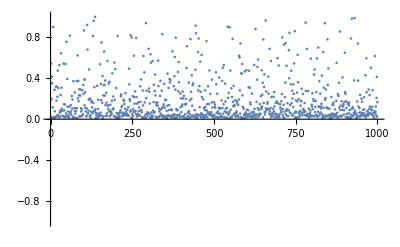

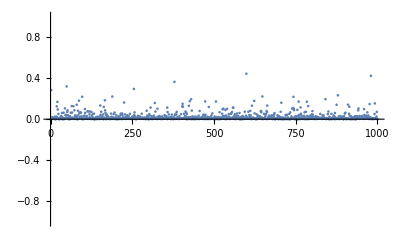

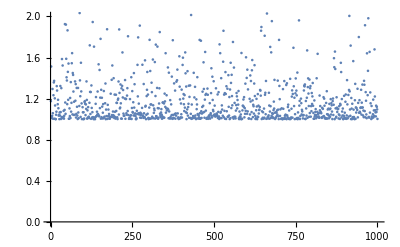

```mathematica
ListPlot[Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}],PlotRange->{-1,1}]
ListPlot[Table[{i,Min[phystest[[i,2]]]},{i,1,Length[cm]}],PlotRange->{-1,1}]
ListPlot[Table[{i,Min[phystest[[i,3]]]},{i,1,Length[cm]}],PlotRange->{0,2}]
```

```mathematica
covmpt=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,-cm[[i]]},{cp[[i]],0,b[[i]],0},{0,-cm[[i]],0,b[[i]]}},{i,10^3}];
```

```mathematica
phystest2={};
Do[AppendTo[phystest2,{Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]//Chop]]}];,{i,1,Length[covmpt]}]


phystest2[[200]]
```

{{135.655,135.655,0.833621,0.833621}}

```mathematica
Table[{i,{Min[phystest2[[i]]]}},{i,1,Length[cm]}];
Min[phystest2[[1]]]
```

0.799579

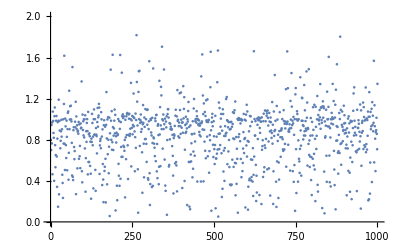

```mathematica
ListPlot[Table[{i,Min[phystest2[[i]]]},{i,10^3}],PlotRange->{0,2}]
```

```mathematica
SympEig={};
Do[AppendTo[SympEig,Min[Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]]]//Chop]];,{i,10^3}];
```

```mathematica
SympEig[[1]]
```

0.799579

```mathematica
Table[{i,{SympEig[[i]]}},{i,10^3}];
```

```mathematica
ListPlot[Table[{i,SympEig[[i]]},{i,10^3}],PlotRange->{0,2}]
```

-Graphics-

```mathematica
Negativity={};
Do[AppendTo[Negativity,(1-SympEig[[i]])/(2SympEig[[i]])];,{i,10^3}];
Negativity[[1]]
```

0.125329

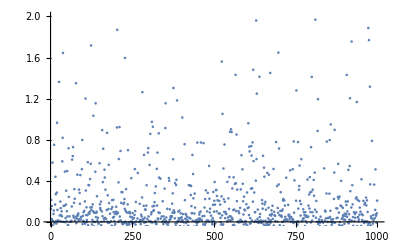

```mathematica
Table[{i,{Negativity[[i]]}},{i,10^3}];
ListPlot[Table[{i,Negativity[[i]]},{i,10^3}],PlotRange->{0,2}]
```

```mathematica
LogNeg={};
Do[AppendTo[LogNeg,-Log[SympEig[[i]]]];,{i,10^3}];
LogNeg[[1]]
```

0.22367

```mathematica
Table[{i,{LogNeg[[i]]}},{i,10^3}];
```

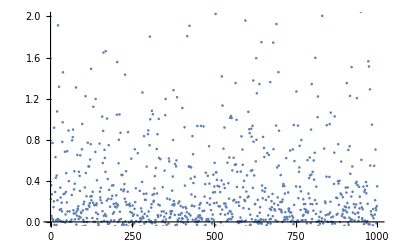

```mathematica
ListPlot[Table[{i,LogNeg[[i]]},{i,10^3}],PlotRange->{0,2}]
```